# RDown Quadratic Fits

## Setup

### Load packages

```mathematica
(* To run this code, you need the RDown.m package. It can be found here: https://github.com/frcojimenez/GW_Rdown/tree/main/codes/Mathematica *)
```

```mathematica
Which[$SystemID=="MacOSX-x86-64",Get["/Users/xisco/git/ah-overtones-project/codes/RDownCode/RDown.m"],$SystemID=="Linux-x86-64",Get["/work/francisco.jimenez/RDFits/RDown.m"]]
```

```mathematica
(* This python-mathematica wrapper must be as well installed. More info. in: https://reference.wolfram.com/language/workflow/ConfigurePythonForExternalEvaluate.html  *)
```

```mathematica
Print["Starting Python session." ,session = StartExternalSession[{"Python","Version"->"3"}]];
ExternalEvaluate[session, "import qnm; import numpy as np; from qnm.schwarzschild.overtonesequence import SchwOvertoneSeq as schw"];
```

Starting Python session.ExternalSessionObject[…]

### Load SXS

```mathematica
index=3
mysxscase={"~/mount/Atlas/SXS/data/SXS_BBH_0305/Lev6"}
```

3

{~/mount/Atlas/SXS/data/SXS_BBH_0305/Lev6}

```mathematica
mysxscasemetafile=FileNames["metadata.json",mysxscase,2][[1]]
metadata=Import[mysxscasemetafile];
h5file=FileNames["*rh*",mysxscase,2]
```

~/mount/Atlas/SXS/data/SXS_BBH_0305/Lev6/metadata.json

{~/mount/Atlas/SXS/data/SXS_BBH_0305/Lev6/rhOverM_Asymptotic_GeometricUnits_CoM.h5}

```mathematica
Print["mass1 = ",mass1=("initial_mass1"/.metadata)]
Print["mass2 = ",mass2=("initial_mass2"/.metadata)]
Print["χ1 = ",χ1=Chop[(("initial_dimensionless_spin1"/.metadata)[[-1]])]]
Print["χ2 = ",χ2=Chop[(("initial_dimensionless_spin2"/.metadata)[[-1]])]]
Print["m1/m2 = ",q=Max[{mass1/mass2,1}]]
Print["m1·m2 = ",η=q/(1+q)^2*1.]
Print["af = ",af=("remnant_dimensionless_spin"/.metadata)[[-1]]]
Print["mf = ",mfa=("remnant_mass"/.metadata)]
Print["Tag = ",tag=StringReplace[("alternative_names"/.metadata),":"->"_"]]
If[Length[tag]==2,tag=tag[[2]]]
```

mass1 = 0.549795

mass2 = 0.450205

χ1 = 0.33

χ2 = -0.44

m1/m2 = 1.22121

m1·m2 = 0.24752

af = 0.692085

mf = 0.952033

Tag = {PRIVATE_BBH_0225,SXS_BBH_0305}

SXS_BBH_0305

```mathematica
sxsrhs=Conjugate/@GetAsymptoticMultiMode[h5file[[-1]],2,modes,"ReSample"->False,"ZeroAlign"->True,"Code"->"SXS"];
```

```mathematica
tmax=TimeOfMaximum[sxsrhs[[1]]];
t0=tmax
mysxscase22modeRD=Select[sxsrhs[[1]],#[[1]]≥ tmax&];
RDdata=Select[mysxscase22modeRD,t0≤#[[1]]≤t0+90&];
```

0.

### Fit Functions

```mathematica
Options[FitRingdownGridαβ]=Join[Options[OvertoneModel],
{"βrange"-> {-2,2},"SpinThresholds"-> {-2,2},
"Iterations"-> 7,"MassStepInit"-> 0.05,"MaxIterations"->1000,
"SpinStepInit"-> 0.05,"MassSampling"-> 20,
"SpinSampling"-> 20,"NeighbourPointsMass"->2,
"NeighbourPointsSpin"->2,"w228data"-> {},"w229data"->{},"ωlmnFunction"-> ωlmnPy,"ExpFactor"->False,
"TrueParameters"->{1,1},"wlmntables"->{},"Verbose"->False,"Tones"->{},"FixTonesBeyond"->"" }];
FitRingdownGridαβ[thedata_,nmax_,{mass_,spin_},thetmin_,alfabetarange_,OptionsPattern[]]:=
Block[{i,data,rest,restTotal={},
αpar,βpar,βval,maxtit,expfactor,pertvars,αval,ampslist,ov,ovmod,ansatzreal,datareal,amin,amax,,mmin,mmax,curDistance,pars,bfmodel,res,
resmin,mode,distancemin,posresmin,posdistancemin,bestmass,bestspin,bestpars,bestbic,Global`t,datam,times,mixing,lenc,lend,
varyω,wc228data,Am,βm,truepars,w228data,w229data,ωlmnfunc,themode,mminInit,mmaxInit,aminInit,amaxInit,athreshmin,athreshmax,mstep,astep,msamp,
asamp,nbneighboursm,nbneighboursa,itmax,tones,tonesbeyond,wlmntables,wlmnctables,wlmnmixtables,verbose,withcounterotating},

w228data=OptionValue["w228data"];
w229data=OptionValue["w229data"];
ωlmnfunc = OptionValue["ωlmnFunction"];
themode = OptionValue["Mode"];
mminInit=alfabetarange[[1]];
mmaxInit=alfabetarange[[2]];

aminInit=OptionValue["βrange"][[1]];
amaxInit=OptionValue["βrange"][[2]];

athreshmin = OptionValue["SpinThresholds"][[1]];
athreshmax = OptionValue["SpinThresholds"][[2]];
mstep=OptionValue["MassStepInit"];
astep=OptionValue["SpinStepInit"];
msamp = OptionValue["MassSampling"];
asamp = OptionValue["SpinSampling"];
nbneighboursm = OptionValue["NeighbourPointsMass"];
nbneighboursa = OptionValue["NeighbourPointsSpin"];
itmax=OptionValue["Iterations"];
tones=OptionValue["Tones"];
tonesbeyond=OptionValue["FixTonesBeyond"];
truepars=OptionValue["TrueParameters"];
wlmntables=OptionValue["wlmntables"];
wlmnctables=OptionValue["wlmnctables"];
wlmnmixtables = OptionValue["wlmnmixtables"];
verbose=OptionValue["Verbose"];
withcounterotating=OptionValue["WithCounterRotating"];

mixing = OptionValue["Mixing"];
varyω=OptionValue["Varyω"];
wc228data=OptionValue["wc228data"];
data=Select[thedata,#[[1]]>=thetmin&];
times=data[[All,1]];
lend=Length[data];
αpar=ToExpression["α"<>ToString@nmax];
βpar=ToExpression["β"<>ToString@nmax];
mode=OptionValue["Mode"];
ansatzreal=OptionValue["AnsatzReal"];
datareal=OptionValue["DataReal"];
expfactor=OptionValue["ExpFactor"];
maxtit=OptionValue["MaxIterations"];

If[ansatzreal,ampslist=Flatten@Table[{ToExpression["x"<>ToString[i]],ToExpression["ϕ"<>ToString[i]]},{i,0,nmax}],ampslist=Flatten@Table[ToExpression["x"<>ToString[i]],{i,0,nmax}]];

If[mixing[[1]],ampslist=Join[ampslist,Table[ToExpression["xm"<>ToString[n]],{n,0,nmax}]]];
If[withcounterotating,ampslist=Join[ampslist,Table[ToExpression["xc"<>ToString[n]],{n,0,nmax}]]];
lenc=Length[ampslist];
ov=OvertoneModel[nmax,{mass,spin},0,"AnsatzReal"->ansatzreal,"Fitα"->{nmax},"Fitτ"-> {nmax},"Mode"->mode,"DataReal"->datareal];
If[expfactor,ov=ov+Am Exp[-βm Global`t];ampslist=Join[ampslist,{{Am,0.001},{βm,0.1}}]];
If[verbose,Print[ampslist]];

For[{i=0;mmin=mminInit;mmax=mmaxInit;amin=aminInit;amax=amaxInit},i<itmax,i++,

If[Not@datareal,
rest=Flatten[Table[

	βval=Round[βval,10.^-15];
	αval=Round[αval,10.^-15];

	ovmod=ov/.αpar->αval/.βpar->βval;
	pars=NonlinearModelFit[data,ovmod,ampslist,Global`t]["BestFitParameters"];
	curDistance=Norm[{αval,βval}-truepars];
	bfmodel=Transpose[{data[[All,1]],ovmod/.pars/.Global`t->times}];
	res=1-EasyMatchT[data,bfmodel,times[[1]],times[[1]]+1000];
	(*res=Total[Abs[bfmodel[[All,2]]-data[[All,2]]]];*)
	
	{αval,βval,res,curDistance,pars},{αval,mmin,mmax,mstep},{βval,amin,amax,astep}],1];,
	
	itmax=1;
	{αpar,βpar}={ToExpression["α"<>ToString[nmax]],ToExpression["β"<>ToString[nmax]]};
	ampslist=Join[ampslist,{{αpar,0},{βpar,0}}];
	ovmod=ov;
	pars=NonlinearModelFit[data,ovmod,ampslist,Global`t,MaxIterations->maxtit]["BestFitParameters"];
	{αval,βval}={αpar/.pars,βpar/.pars};
	curDistance=Norm[{αval,βval}-truepars];
	bfmodel=Transpose[{data[[All,1]],ovmod/.pars/.Global`t->times}];
	(*res=1-EasyMatchT[data,bfmodel,times[[1]],times[[1]]+1000]*);
	res=Total[Abs[bfmodel[[All,2]]-data[[All,2]]]];
	rest={{αval,βval,res,curDistance,pars}};
	];

restTotal=Join[restTotal,rest[[;;,;;4]]];
resmin=Min[rest[[All,3]]];

distancemin=If[i==0,Min[rest[[All,3]]],Min[distancemin,Min[rest[[All,3]]]]];
posresmin=Position[rest[[All,3]],_?(#==resmin&)];
posdistancemin=Position[rest[[All,3]],_?(#==distancemin&)];
bestmass=rest[[posresmin[[1,1]],1]];
bestspin=rest[[posresmin[[1,1]],2]];
bestpars=rest[[posresmin[[1,1]],5]];

If[bestmass==mmin||bestmass==mmax,Print[Style["Warning! Mass hit an edge (iteration "<>ToString[i+1]<>" of "<>ToString[itmax]<>").",Orange]]];
If[bestspin==amin||bestspin==amax||bestspin==athreshmin||bestspin==athreshmax,Print[Style["Warning! Spin hit an edge (iteration "<>ToString[i+1]<>" of "<>ToString[itmax]<>").",Orange]]];

mmin=Max[bestmass-nbneighboursm*mstep,mminInit];
mmax=Min[bestmass+nbneighboursm*mstep,mmaxInit];
amin=Max[bestspin-nbneighboursa*astep,athreshmin,aminInit];
amax=Min[bestspin+nbneighboursa*astep,athreshmax,amaxInit];
If[verbose,Print[" α: ",bestmass," β : ",bestspin,"  α step: ",mstep,"  β step:  ",astep, "  res : ",resmin]];
If[i<itmax-1,mstep=mstep*2.*nbneighboursm/msamp;
astep=astep*2.*nbneighboursa/asamp;]];

restTotal=Sort[DeleteDuplicatesBy[restTotal,#[[1;;2]]&]];
ov=OvertoneModel[nmax,{bestmass,bestspin},0,"Fitα"->{},"Mode"->{2,2},"SpinWeight"->-2,"ωlmnFunction"->ωlmnfunc,"Interpolateωτ"->False,"ReIm"->False,"wlmntables"->wlmntables,"Mixing"->mixing,"wlmnmixtables"->wlmnmixtables];
bfmodel=Transpose[{times,ov/.bestpars/.Global`t->times}];
bestbic = lend + lend *Log[2π]+Log[lend]*(2*lenc+1)+lend *Log[Total@(Abs[bfmodel[[All,2]]-data[[All,2]]]^2)/lend];
{restTotal,bestmass,bestspin,resmin,bestpars}
]
```

## Fits on the 44 new

#### Comparing CNMinimize with grid

```mathematica
(* expected values *)
nmax=1;
qmode440=ωlmnPy[2,2,0,mfa,af]/.{xx_,yy_}->{2xx,2/yy}
lmode44n=(ωlmnPy[4,4,nmax,mfa,af]/.{xx_,yy_}->{xx,1/yy})

(* 44 data *)
index=3;
tmax=TimeOfMaximum[sxsrhs[[index]]];
data=Select[sxsrhs[[index]],#[[1]]≥ tmax&]/.{xx_,yy_}->{xx-tmax,yy};
```

{1.11156,0.170345}

{1.1881,0.267138}

```mathematica
(* fit *)
tab=Table[
tmatchend=200;
RDdata=Select[data,#[[1]]≥i&];
res=FitRingdownGridαβ[RDdata,nmax,{mfa,af},0,{-0.2,0.2},"AnsatzReal"->False,"Mode"->{4,4},"Verbose"->True,"βrange"->{-0.99,0},"Iterations"->7];
qmode=(res[[2;;3]]+1)*lmode44n;
ωdiff=Norm[(qmode-qmode440)/qmode440];
{i,ωdiff},{i,15,15,3}];
```

{x0,x1}

α: -0.1 β : -0.24  α step: 0.05  β step:  0.05  res : 0.0000211264

α: -0.1 β : -0.24  α step: 0.01  β step:  0.01  res : 0.0000211264

α: -0.1 β : -0.24  α step: 0.002  β step:  0.002  res : 0.0000211264

α: -0.1 β : -0.2392  α step: 0.0004  β step:  0.0004  res : 0.0000211184

α: -0.09992 β : -0.23912  α step: 0.00008  β step:  0.00008  res : 0.0000211167

α: -0.09992 β : -0.239152  α step: 0.000016  β step:  0.000016  res : 0.0000211167

α: -0.0999168 β : -0.239155  α step: 3.2×10^-6  β step:  3.2×10^-6  res : 0.0000211167

```mathematica
ωdiff
```

0.196861

```mathematica
ansq44=OvertoneModel[nmax,{mfa,af},0,"AnsatzReal"->True,"Fitα"->{nmax},"Fitτ"-> {nmax},"Mode"->{4,4},"DataReal"->False]
```

ⅇ^(-0.0888605 t) x0 (Cos[1.19294 t+ϕ0]+ⅈ Sin[1.19294 t+ϕ0])+ⅇ^(-0.267138 t (1+β1)) x1 (Cos[1.1881 t (1+α1)+ϕ1]+ⅈ Sin[1.1881 t (1+α1)+ϕ1])

```mathematica
sol=CNMinimize[RDdata[[All,2]],ansq44,{x0,ϕ0,x1,ϕ1,α1,β1},{t,RDdata[[All,1]]}]
```

{2.61442×10^-7,{x0→0.0295083,ϕ0→-1.25545,x1→-0.145937,ϕ1→5.20031,α1→-0.0999011,β1→-0.239171}}

```mathematica
qmode=(({α1,β1}/.sol[[2]])+1)*lmode44n;
ωdiff=Norm[(qmode-qmode440)/qmode440]
```

0.196833

```mathematica
Sqrt[((qmode[[1]]-qmode440[[1]])/qmode440[[1]])^2+((qmode[[2]]-qmode440[[2]])/qmode440[[2]])^2]
```

0.196833

#### Running on t with n=1

```mathematica
(* expected values *)
nmax=1;
qmode440=ωlmnPy[2,2,0,mfa,af]/.{xx_,yy_}->{2xx,2/yy}
lmode44n=(ωlmnPy[4,4,nmax,mfa,af]/.{xx_,yy_}->{xx,1/yy})

(* 44 data *)
index=3;
tmax=TimeOfMaximum[sxsrhs[[index]]];
data=Select[sxsrhs[[index]],#[[1]]≥ tmax&]/.{xx_,yy_}->{xx-tmax,yy};
```

{1.11156,0.170345}

{1.1881,0.267138}

```mathematica
(* fit. I add a shift later of 3.5 units *)
tabn1=Table[
tmatchend=200;
RDdata=Select[data,#[[1]]≥i&];
res=FitRingdownGridαβ[RDdata,nmax,{mfa,af},0,{-0.2,0.2},"AnsatzReal"->False,"Mode"->{4,4},"Verbose"->False,"βrange"->{-0.99,0},"Iterations"->7];
qmode=(res[[2;;3]]+1)*lmode44n;
ωdiff=Norm[(qmode-qmode440)/qmode440];
{i,ωdiff},{i,6,32,1}];
```

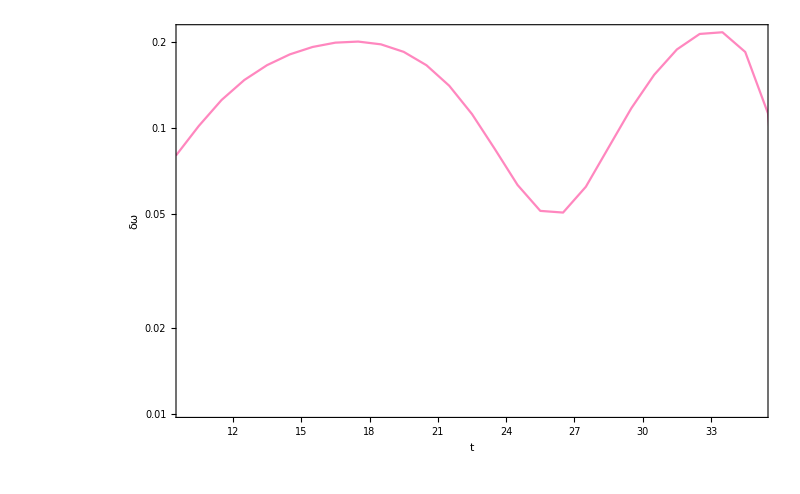

```mathematica
ListLogPlot[Join[tab2,tab]/.{xx_,yy_}->{xx+3.5,yy},PlotRange->{{10,35},All},Joined->True,PlotStyle->colors,Frame->True,LabelStyle->{FontFamily->"Arial",20,GrayLevel[0],Bold},Axes->True,FrameLabel->{"t","δω"},ImageSize->800,FrameStyle->Directive[FontFamily->"Arial",22,GrayLevel[0],Bold]]
```

#### Running on t with n=2

```mathematica
(* expected values *)
nmax=2;
qmode440=ωlmnPy[2,2,0,mfa,af]/.{xx_,yy_}->{2xx,2/yy}
lmode44n=(ωlmnPy[4,4,nmax,mfa,af]/.{xx_,yy_}->{xx,1/yy})

(* 44 data *)
index=3;
tmax=TimeOfMaximum[sxsrhs[[index]]];
data=Select[sxsrhs[[index]],#[[1]]≥ tmax&]/.{xx_,yy_}->{xx-tmax,yy};
```

{1.11156,0.170345}

{1.17875,0.447027}

```mathematica
(* fit *)
tabn2=Table[
tmatchend=200;
RDdata=Select[data,#[[1]]≥i&];
res=FitRingdownGridαβ[RDdata,nmax,{mfa,af},0,{-0.2,0.2},"AnsatzReal"->False,"Mode"->{4,4},"Verbose"->False,"βrange"->{-0.99,0},"Iterations"->7];
qmode=(res[[2;;3]]+1)*lmode44n;
ωdiff=Norm[(qmode-qmode440)/qmode440];
{i,ωdiff},{i,6,32,2}];
```

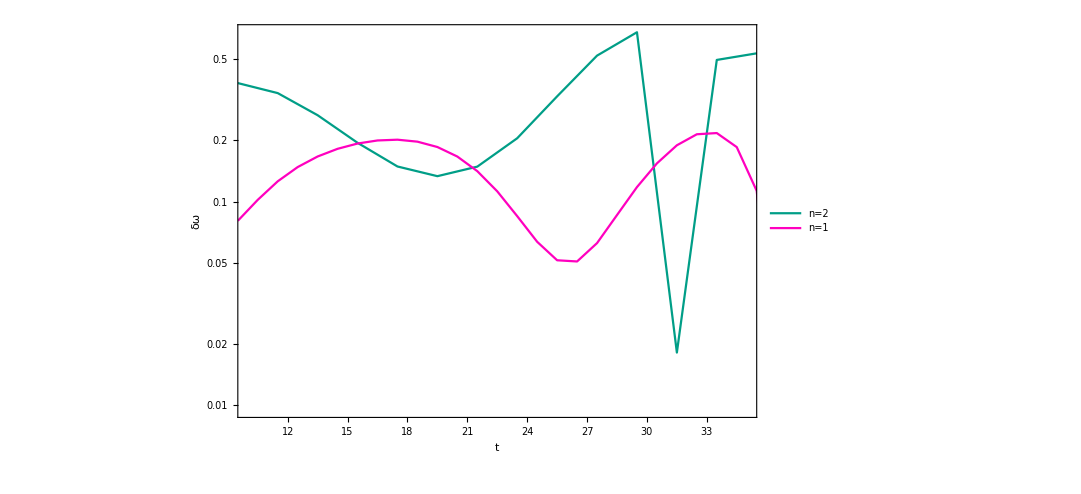

```mathematica
ListLogPlot[{tabn2/.{xx_,yy_}->{xx+3.5,yy},Join[tab2,tab]/.{xx_,yy_}->{xx+3.5,yy}},PlotRange->{{10,35},All},Joined->True,PlotStyle->colors,PlotLegends->{"n=2","n=1"},Frame->True,LabelStyle->{FontFamily->"Arial",20,GrayLevel[0],Bold},Axes->True,FrameLabel->{"t","δω"},ImageSize->800,FrameStyle->Directive[FontFamily->"Arial",22,GrayLevel[0],Bold]]
```